# fraction overlap

## 2 dimensions

area of overlap as function of distance from optimum (d) and angle between optima (θ) [this uses the fact that the distance between the circle centres, x, is determined by d and θ in our case]

```mathematica
A[d_,θ_]:=2 d^2 ArcCos[x/(2d)]-x/2  √(4 d^2-x^2)/.x->d √(2(1-Cos[θ]))
```

overlap declines with angle (here from 0 to 180 degrees) for any distance

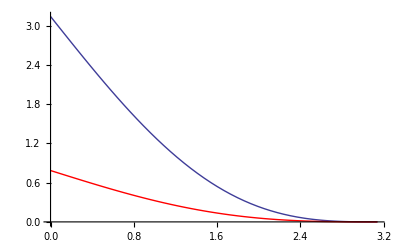

```mathematica
Show[
Plot[A[d,θ]/.d->1,{θ,0,π}],
Plot[A[d,θ]/.d->0.5,{θ,0,π},PlotStyle->Red],
PlotRange->All
]
```

overlap increases with distance for any angle

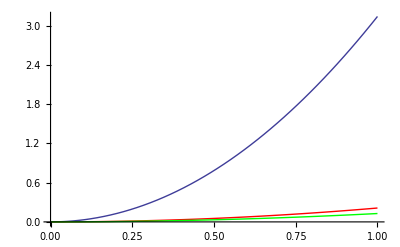

```mathematica
Show[
Plot[A[d,θ]/.θ->0,{d,0,1}],
Plot[A[d,θ]/.θ->90,{d,0,1},PlotStyle->Red],
Plot[A[d,θ]/.θ->180,{d,0,1},PlotStyle->Green],
PlotRange->All
]
```

but note that the fraction overlap is independent of the distance, d:

```mathematica
fA=Simplify[A[d,θ]/A[d,0],d>0]
```

(2 ArcCos[√(Sin[θ/2]^2)]-√(Sin[θ]^2))/π

and declines from 1 to 0 with angle

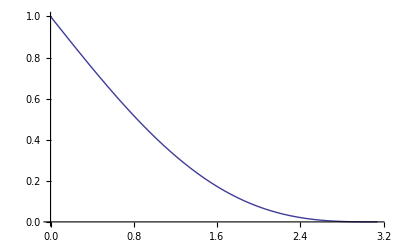

```mathematica
Show[
Plot[A[d,θ]/A[d,0]/.d->1,{θ,0,π}],
PlotRange->All
]
```

the fraction overlap is 0 when the angle is 180 degrees

```mathematica
A[d,θ]/A[d,0]/.θ->π
```

0

there is perfect overlap when the angle is 0

```mathematica
A[d,θ]/A[d,0]/.θ->0
```

1

distance and fraction overlap as functions of angle

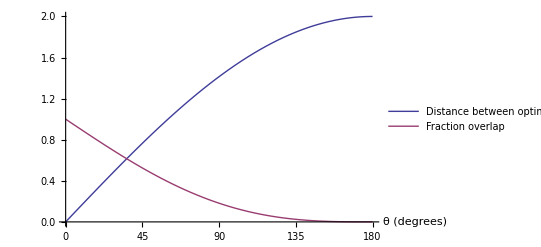

```mathematica
Plot[
{
d*√(2(1-Cos[θ*π/180]))/.d->1,
A[d,θ*π/180]/A[d,0]/.d->1
},
{θ,0,180},
Ticks->{{0,45,90,135,180},Automatic},
AxesLabel->{"θ (degrees)"},
PlotLegends->{"Distance between optima","Fraction overlap"}
]
```

fraction overlap as function of distance from optimum (d) and distance between circle centres (x) [together these determine the angle between optima]

```mathematica
A[x_,d_]:=2 d^2 ArcCos[x/(2d)]-x/2  √(4 d^2-x^2)
```

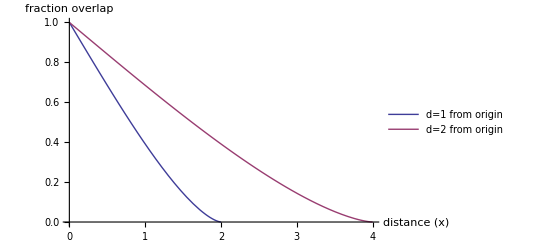

```mathematica
Plot[{A[x,d]/A[0,d]/.d->1,A[x,d]/A[0,d]/.d->2},{x,0,4},AxesLabel->{"distance (x)","fraction overlap"},
PlotLegends->{"d=1 from origin","d=2 from origin"}]
```

## 3 dimensions

http://mathworld.wolfram.com/Sphere-SphereIntersection.html

volume overlap bw spheres of radii r and R, with distance d between the centres

```mathematica
(π (R+r-d)^2(d^2+2d r-3 r^2+2d R+6r R-3 R^2))/(12d);
```

when both have same radii

```mathematica
%/.R->r//Simplify
```

1/12 π (d-2 r)^2 (d+4 r)

and when the distance between them is determined by the distance from the origin (also r) and the angle between them

```mathematica
V[r_,θ_]:=1/12 π (d-2 r)^2 (d+4 r)/.d->r √(2(1-Cos[θ]))
```

then the fraction overlap is

```mathematica
fV=V[r,θ]/V[r,0]//Simplify
```

1/16 (-2+√(2-2 Cos[θ]))^2 (4+√(2-2 Cos[θ]))

which is independent of the distance to the optimum, r, and declines with angle

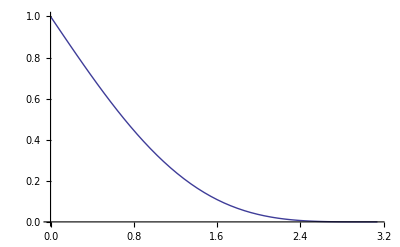

```mathematica
Plot[fV,{θ,0,π}]
```

Comparing to the 2 dimensional case

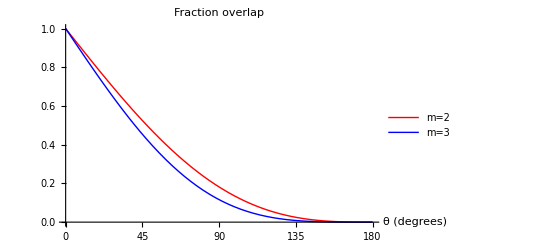

```mathematica
Plot[{fA/.θ->deg*π/180,fV/.θ->deg*π/180},{deg,0,180},PlotStyle->{{Red},{Blue}},
Ticks->{{0,45,90,135,180},Automatic},
AxesLabel->{"θ (degrees)"},
PlotLegends->{"m=2","m=3"},
PlotLabel->"Fraction overlap"
]
```

we see that the volume overlap (m=3) decreases even faster than the area overlap

## m dimensions

```mathematica
Clear[c1,c2,V]
```

Here we are interested in the volume of the intersection between two m-dimensional spheres, with centres at distance d, with radii r1 and r2. We follow Matt’s answer at https://math.stackexchange.com/questions/162250/how-to-compute-the-volume-of-intersection-between-two-hyperspheres

The volume of the intersection is the volume of two spherical caps, glued at a hyperplane.

The heights of the cap bases are

```mathematica
c1[d_,r1_,r2_]:=(d^2+r1^2-r2^2)/(2d)
```

```mathematica
c2[d_,r1_,r2_]:=(d^2-r1^2+r2^2)/(2d)
```

Computing the volume of these caps requires some fancy integration ( Concise Formulas for the Area and Volume of a Hyperspherical Cap, Shengqiao Li, Asian Journal of Mathematics and Statistics 4(1), 66-70, 2011). Turns out the volume of a cap is

```mathematica
V[m_,r_,a_]:=If[a≥0,1/2 π^(m/2)/Gamma[m/2+1] r^m BetaRegularized[1-a^2/r^2,(m+1)/2,1/2],π^(m/2)/Gamma[m/2+1] r^m-1/2 π^(m/2)/Gamma[m/2+1] r^m BetaRegularized[1-a^2/r^2,(m+1)/2,1/2]]
```

where a is the height of the cap base.

Thus the volume of the intersection is

```mathematica
Vint=V[m,r1,c1[d,r1,r2]]+V[m,r2,c2[d,r1,r2]];
```

and in our case we want both spheres to have the same radii, and the distance to depend on that radius and the angle between them (which we can restrict between 0 and 180 because 180 to 360 is just the same thing)

```mathematica
VintUs=Simplify[Vint/.r1->r/.r2->r/.d->r √(2(1-Cos[θ])),{r>0,m>0,0≤θ≤π}]
```

(π^(m/2) r^m BetaRegularized[Cos[θ/2]^2,(1+m)/2,1/2])/Gamma[1+m/2]

It looks like things are working (check areas/volumes of circle/sphere)

```mathematica
VintUs/.θ->0/.m->{2,3}
```

{π r^2,(4 π r^3)/3}

and no overlap if angle is 180deg

```mathematica
Simplify[VintUs/.θ->π,{r>0,m>0}]
```

0

Then the fraction overlap is

```mathematica
Vfraction=Simplify[VintUs/(VintUs/.θ->0),m≥1]
```

BetaRegularized[Cos[θ/2]^2,(1+m)/2,1/2]

```mathematica
Simplify[BetaRegularized[1,(1+m)/2,1/2],m≥1]
```

1

which is independent of r

Compare with previous results (m=2,3) to ensure consistent

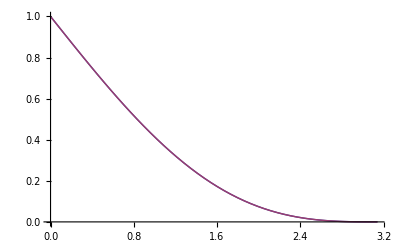

```mathematica
Plot[{Vfraction/.m->2,(2 ArcCos[√(Sin[θ/2]^2)]-√(Sin[θ]^2))/π},{θ,0,π}]
```

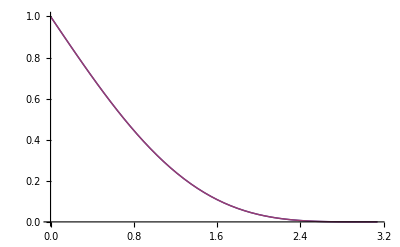

```mathematica
Plot[{Vfraction/.m->3,1/16 (-2+√(2-2 Cos[θ]))^2 (4+√(2-2 Cos[θ]))},{θ,0,π}]
```

And now we can clearly see the effect of dimensionality

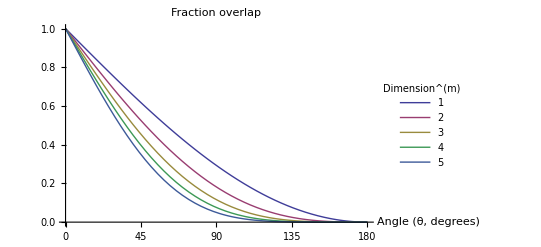

```mathematica
nms=5;
Plot[Evaluate@Table[Vfraction/.θ->θ π/180,{m,1,nms}],
{θ,0,180},
PlotLegends->Placed[LineLegend[Table[m,{m,1,nms}],LegendLabel->"Dimension^(m)"],Scaled@{0.85,0.6}],
Ticks->{{0,45,90,135,180},Automatic},
AxesLabel->{"Angle (θ, degrees)"},
PlotLabel->"Fraction overlap"]
```

Solve for angle as a function of distance between hypersphere centres

```mathematica
Solve[x==d √(2(1-Cos[θ])),θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-ArcCos[(2 d^2-x^2)/(2 d^2)]},{θ→ArcCos[(2 d^2-x^2)/(2 d^2)]}}

and plot fraction overlap as function of distance between optima

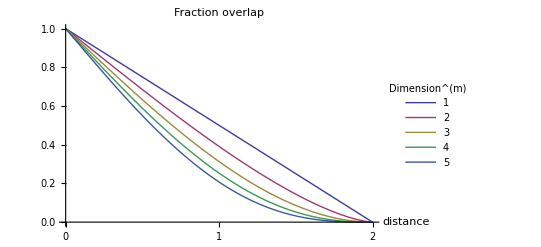

```mathematica
nms=5;
Plot[Evaluate@Table[Vfraction/.θ->ArcCos[(2 d^2-x^2)/(2 d^2)]/.d->1,{m,1,nms}],
{x,0,2},
PlotLegends->Placed[LineLegend[Table[m,{m,1,nms}],LegendLabel->"Dimension^(m)"],Scaled@{0.85,0.6}],
Ticks->{{0,1,2},Automatic},
AxesLabel->{"distance"},
PlotLabel->"Fraction overlap"]
```

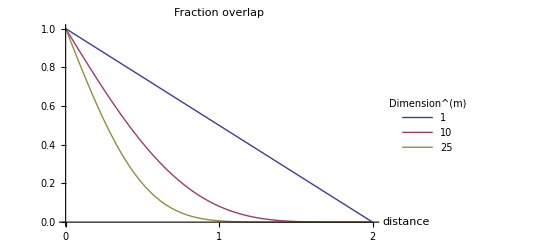

```mathematica
Plot[Evaluate@Table[Vfraction/.θ->ArcCos[(2 d^2-x^2)/(2 d^2)]/.d->1,{m,{1,10,25}}],
{x,0,2},
PlotLegends->Placed[LineLegend[Table[m,{m,{1,10,25}}],LegendLabel->"Dimension^(m)"],Scaled@{0.85,0.6}],
Ticks->{{0,1,2},Automatic},
AxesLabel->{"distance"},
PlotLabel->"Fraction overlap"]
```

## over the walk (fraction of beneficial phenotypic space that is mutually beneficial)

```mathematica
Clear[c1,c2,V]
```

Here we are interested in the volume of the intersection between two m-dimensional spheres, with centres at distance d, with radii r1 and r2. We follow Matt’s answer at https://math.stackexchange.com/questions/162250/how-to-compute-the-volume-of-intersection-between-two-hyperspheres

The volume of the intersection is the volume of two spherical caps, glued at a hyperplane.

The heights of the cap bases are

```mathematica
c1[d_,r1_,r2_]:=(d^2+r1^2-r2^2)/(2d)
```

```mathematica
c2[d_,r1_,r2_]:=(d^2-r1^2+r2^2)/(2d)
```

Computing the volume of these caps requires some fancy integration ( Concise Formulas for the Area and Volume of a Hyperspherical Cap, Shengqiao Li, Asian Journal of Mathematics and Statistics 4(1), 66-70, 2011). Turns out the volume of a cap is

```mathematica
V[m_,r_,a_]:=If[a≥0,1/2 π^(m/2)/Gamma[m/2+1] r^m BetaRegularized[1-a^2/r^2,(m+1)/2,1/2],π^(m/2)/Gamma[m/2+1] r^m-1/2 π^(m/2)/Gamma[m/2+1] r^m BetaRegularized[1-a^2/r^2,(m+1)/2,1/2]]
```

where a is the height of the cap base.

Thus the volume of the intersection is

```mathematica
Vint=V[m,r1,c1[d,r1,r2]]+V[m,r2,c2[d,r1,r2]];
```

and in our case we want both spheres to have the same radii, and the distance to depend on that radius and the angle between them (which we can restrict between 0 and 180 because 180 to 360 is just the same thing). The distance between the optima is d0 √(2(1-Cos[θ])) where d0 is the initial distance to an optimum and the radii are equal (we call them d, the distance to the optima)

```mathematica
VintUs=Simplify[Vint/.d->d0 √(2(1-Cos[θ]))/.r1->d/.r2->d,{d>0,m>0,0≤θ≤π,d0>0}]
```

(d^m π^(m/2) BetaRegularized[1+(d0^2 (-1+Cos[θ]))/(2 d^2),(1+m)/2,1/2])/Gamma[1+m/2]

It looks like things are working (check areas/volumes of circle/sphere)

```mathematica
VintUs/.θ->0/.m->{2,3}
```

{d^2 π,(4 d^3 π)/3}

and no overlap if angle is 180deg and we are at the initial step

```mathematica
Simplify[VintUs/.θ->π/.d->d0,{d>0,m>0}]
```

0

Then the fraction overlap is

```mathematica
Vfraction=Simplify[VintUs/(VintUs/.θ->0)/.d->(1-f) d0,m≥1]
```

BetaRegularized[1+(-1+Cos[θ])/(2 (-1+f)^2),(1+m)/2,1/2]

where f is the fraction of the initial distance that has been traversed.

Plot the fraction overlap as a function of the fraction traversed

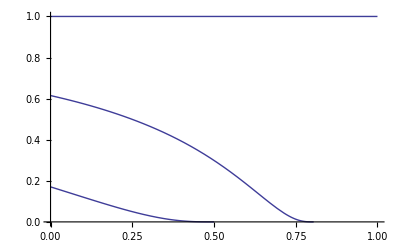

```mathematica
Plot[Vfraction/.θ->{0,π/8,π/3}/.m->6,{f,0,1},PlotRange->All]
```

And we see that the fraction overlap starts lower and declines to zero for angles less than 0.

If we could integrate this over f we would have a single value (avg overlap over the walk) but alas:

```mathematica
Integrate[Vfraction,{f,0,1}]
```

∫_0^1 BetaRegularized[1+(-1+Cos[θ])/(2 (-1+f)^2),(1+m)/2,1/2]/BetaRegularized[1,(1+m)/2,1/2]ⅆf

## over the walk (fraction of beneficial mutations that are mutually beneficial)

```mathematica
Clear[c1,c2,V]
```

Here we are interested in the volume of the intersection between two m-dimensional spheres, with centres at distance d, with radii r1 and r2. We follow Matt’s answer at https://math.stackexchange.com/questions/162250/how-to-compute-the-volume-of-intersection-between-two-hyperspheres

The volume of the intersection is the volume of two spherical caps, glued at a hyperplane.

The heights of the cap bases are

```mathematica
c1[d_,r1_,r2_]:=(d^2+r1^2-r2^2)/(2d)
```

```mathematica
c2[d_,r1_,r2_]:=(d^2-r1^2+r2^2)/(2d)
```

Computing the volume of these caps requires some fancy integration ( Concise Formulas for the Area and Volume of a Hyperspherical Cap, Shengqiao Li, Asian Journal of Mathematics and Statistics 4(1), 66-70, 2011). Turns out the volume of a cap is

```mathematica
V[m_,r_,a_]:=If[a≥0,1/2 π^(m/2)/Gamma[m/2+1] r^m BetaRegularized[1-a^2/r^2,(m+1)/2,1/2],π^(m/2)/Gamma[m/2+1] r^m-1/2 π^(m/2)/Gamma[m/2+1] r^m BetaRegularized[1-a^2/r^2,(m+1)/2,1/2]]
```

where a is the height of the cap base.

Thus the volume of the intersection is

```mathematica
Vint=V[m,r1,c1[d,r1,r2]]+V[m,r2,c2[d,r1,r2]];
```

In our case we will assume both populations adapt at the same speed and thus both hyperspheres have the same radii. The distance between the centres of the hyperspheres depends on that radius and the angle between them θ (which we can restrict between 0 and 180 because 180 to 360 is just the same thing). The distance between the centres begins as d0 √(2(1-Cos[θ])) where d0 is the initial distance from the mean ancestor phenotype to an optimum. This is reduced as the populations adapt. If we let f the the fraction of adaptation completed, the distance between the centres is d0(1-f)√(2(1-Cos[θ])) and the radius of the hyperspheres is d0(1-f)

```mathematica
VintUs=Simplify[Vint/.d->d √(2(1-Cos[θ]))/.r1->d/.r2->d,{d>0,m>0,0≤θ≤π,d0>0,0≤f≤1}]
```

(d^m π^(m/2) BetaRegularized[Cos[θ/2]^2,(1+m)/2,1/2])/Gamma[1+m/2]

It looks like things are working (check areas/volumes of circle/sphere)

```mathematica
VintUs/.θ->0/.m->{2,3}
```

{d^2 π,(4 d^3 π)/3}

and no overlap if angle is 180deg and we are at the initial step

```mathematica
Simplify[VintUs/.θ->π/.d->d0,{d>0,m>0}]
```

0

Then the fraction overlap is

```mathematica
Vfraction=Simplify[VintUs/(VintUs/.θ->0)/.d->(1-f) d0,m≥1]
```

BetaRegularized[Cos[θ/2]^2,(1+m)/2,1/2]

which is the same regardless of how far adaptation has proceeded (which makes sense since adaptation essentially just reduces the distance to the optima, and the fraction of overlap is independent of this distance - in effect, as the overlap gets smaller so too does the radii and thus the volume of the hyperspheres, and these cancel out).

# joint fixation

## weight by s - parallel evoltion (angle=0)

Let the selection coefficient of a mutant be its log fitness minus the log fitness of its ancestor. When the ancestor is at the origin, fitness is a Gaussian with max at (xopt,yopt), the selection coefficient of a mutant at (x,y) is

```mathematica
s[x_,y_]:=-((x-xopt)^2+(y-yopt)^2)/2- -((0-xopt)^2+(0-yopt)^2)/2
```

Beneficial mutations (s>0) lie in a circle centered at (xopt, yopt) with radius d, where d is the distance from the origin to the optimum. When d is small enough such that all beneficial mutants are weakly selected

```mathematica
s[xopt,yopt];
%/.xopt->d Cos[θ]/.yopt->d Sin[θ];
%<1//Simplify
```

d^2<2

then we can approximate the probability of fixation by 2s. Integrating uniformly over the circle of beneficial mutations gives the average probability of fixation of beneficial mutations (given they exist) at the beginning of the adaptive walk (ie in the wildtype background)

```mathematica
Simplify[Integrate[Simplify[Integrate[2s[x,y],{y,-√(d^2-x^2+2 x xopt-xopt^2)+yopt,√(d^2-x^2+2 x xopt-xopt^2)+yopt}]],{x,xopt-d,xopt+d}],{d>0}];
%/.xopt->d Cos[θ]/.yopt->d Sin[θ];
%//Simplify
```

(d^4 π)/2

Under parallel selection (ie same optimum) the probability of joint fixation is

```mathematica
Simplify[Integrate[Simplify[Integrate[2s[x,y]2s[x,y],{y,-√(d^2-x^2+2 x xopt-xopt^2)+yopt,√(d^2-x^2+2 x xopt-xopt^2)+yopt}]],{x,xopt-d,xopt+d}],{d>0}];
%/.xopt->d Cos[θ]/.yopt->d Sin[θ];
%//Simplify
```

(d^6 π)/3

Extensions:
1) non-parallel selection
2) mutation-selection balance
3) adaptive walk

## weight by s (any angle)

Let the selection coefficient of a mutant be its log fitness minus the log fitness of its ancestor. When the ancestor is at the origin, fitness is a Gaussian with max at (xopt,yopt), the selection coefficient of a mutant at (x,y) is

```mathematica
s[x_,y_,xopt_,yopt_]:=-((x-xopt)^2+(y-yopt)^2)/2- -((0-xopt)^2+(0-yopt)^2)/2
```

Beneficial mutations (s>0) lie in a circle centered at (xopt, yopt) with radius d, where d is the distance from the origin to the optimum. When d is small enough such that all beneficial mutants are weakly selected

```mathematica
s[xopt,yopt,xopt,yopt];
%/.xopt->d Cos[θ]/.yopt->d Sin[θ];
%<1//Simplify
```

d^2<2

then we can approximate the probability of fixation by 2s. Integrating uniformly over the circle of beneficial mutations gives the average probability of fixation of beneficial mutations (given they exist) at the beginning of the adaptive walk (ie in the wildtype background)

```mathematica
Simplify[Integrate[Simplify[Integrate[2s[x,y,xopt,yopt],{y,-√(d^2-x^2+2 x xopt-xopt^2)+yopt,√(d^2-x^2+2 x xopt-xopt^2)+yopt}]],{x,xopt-d,xopt+d}],{d>0}];
%/.xopt^2+yopt^2->d^2//Simplify
```

(d^4 π)/2

We can also ask what the probability two populations that differ in their optima fix the same mutation. We cannot use 2s 2s and integrate over one circle because one of the s’s will be negative over parts of that circle. We could use 1-Exp[-2s], but we can’t even do that for one population

```mathematica
Simplify[Integrate[Simplify[Integrate[(1-Exp[-2s[x,y,xopt,yopt]]),{y,-√(d^2-x^2+2 x xopt-xopt^2)+yopt,√(d^2-x^2+2 x xopt-xopt^2)+yopt}]],{x,xopt-d,xopt+d}],{d>0}];
%/.xopt^2->d^2-yopt^2//Simplify
```

∫_(-d+xopt)^(d+xopt) (2 √(d^2-(x-xopt)^2)-ⅇ^(x^2-2 x xopt-yopt^2) √π Erfi[√(d^2-(x-xopt)^2)])ⅆx

Another option would be to just integrate over the fraction of overlap, but we don’t yet have a good equation for that. 

A final option is to just numerically integrate. Let d be the Euclidean distance of the optima from the origin. Let θ be the angle between optima, connected through the origin. Since we are doing things numerically we can just use the full 1-Exp[-2s] instead of 2s. First check this is working by comparing to the 2s and θ=0 results above

```mathematica
xopt=d;
yopt=0;
xopt2=d Cos[θ];
yopt2=d Sin[θ];
d=0.5;
θ=0;

(1-Exp[-2s[x,y,xopt,yopt]])(1-Exp[-2s[x,y,xopt2,yopt2]])//Simplify;
(*(2s[x,y,xopt,yopt])2s[x,y,xopt2,yopt2]//Simplify;*)
NIntegrate[%,{x,xopt-d,xopt+d},{y,yopt-√(d^2-(x-xopt)^2),yopt+√(d^2-(x-xopt)^2)}]
(d^6 π)/3.(*check for θ=0 and 2s approx*)
Clear[d,θ,xopt,yopt,xopt2,yopt2]
```

0.0136227

0.0163625

And now we can plot this over θ for a given d

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

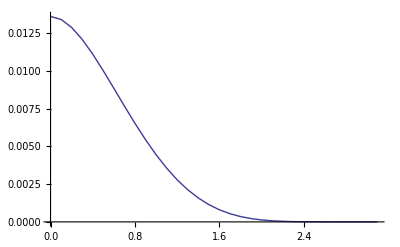

```mathematica
xopt=d;
yopt=0;
xopt2=d Cos[θ];
yopt2=d Sin[θ];
d=0.5;

(1-Exp[-2s[x,y,xopt,yopt]])(1-Exp[-2s[x,y,xopt2,yopt2]])//Simplify;

Table[
{θ,
NIntegrate[
%HeavisideTheta[s[x,y,xopt2,yopt2]],
{x,xopt-d,xopt+d},
{y,yopt-√(d^2-(x-xopt)^2),yopt+√(d^2-(x-xopt)^2)}
]
},
{θ,0,π,0.1}];
ListPlot[%,Joined->True]

Clear[d,θ,xopt,yopt,xopt2,yopt2]
```

# vary d’s between populations with theta constant

Let’s relax the assumption that both populations have the same radius and instead assume, without loss of generality, that r1 is the population with the smaller radius, i.e., R= r2/r1>1. Then the volume of overlap is

```mathematica
VintUsTheta=Simplify[Vint/.d->√((r2 Cos[θ]-r1)^2+(r2 Sin[θ])^2)/.r2-> R r1,{r1>0,R>1,m>0,0≤θ≤π}]
```

Piecewise[{{(π^(m/2) ((R r1)^m BetaRegularized[Sin[θ]^2/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]-r1^m (-2+BetaRegularized[(R^2 Sin[θ]^2)/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2])))/(2 Gamma[1+m/2]), R Cos[θ]>1}, {(π^(m/2) ((R r1)^m BetaRegularized[Sin[θ]^2/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]+r1^m BetaRegularized[(R^2 Sin[θ]^2)/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]))/(2 Gamma[1+m/2]), True}}]

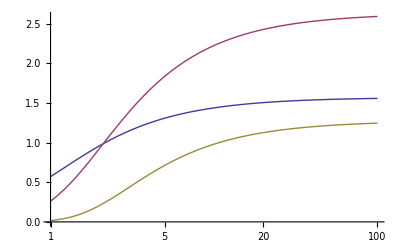

```mathematica
VintUsTheta/.m->{2,5,10}/.θ->π/2/.r1->1;
LogLinearPlot[%,{R,1,100}]
```

The volumes of the spheres are

```mathematica
V1=Simplify[VintUs/.r1->r1/.r2->r1]/.θ->0;
V2=Simplify[VintUs/.r1->r2/.r2->r2]/.θ->0;
```

Thus the volume of overlap divided by the volume of sphere 1 (fraction of overlap for pop1) is

```mathematica
F01=Simplify[VintUsTheta/V1,{r1>0,m>0,R>1,0≤θ≤π}]
```

Piecewise[{{1/2 (2+R^m BetaRegularized[Sin[θ]^2/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]-BetaRegularized[(R^2 Sin[θ]^2)/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]), R Cos[θ]>1}, {1/2 (R^m BetaRegularized[Sin[θ]^2/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]+BetaRegularized[(R^2 Sin[θ]^2)/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]), True}}]

and for population 2

```mathematica
F02=Simplify[Simplify[VintUsTheta/V2/.R->r2/r1/.r1->Rinv r2,{r2>0,m>0,R>1,0≤θ≤π}]/.Rinv->1/R,{R>1}]
```

Piecewise[{{1/2 R^-m (2+R^m BetaRegularized[Sin[θ]^2/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]-BetaRegularized[(R^2 Sin[θ]^2)/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]), R Cos[θ]>1}, {1/2 (BetaRegularized[Sin[θ]^2/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]+R^-m BetaRegularized[(R^2 Sin[θ]^2)/(1+R^2-2 R Cos[θ]),(1+m)/2,1/2]), True}}]

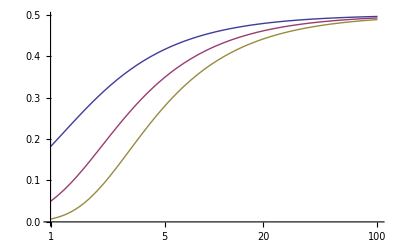

```mathematica
{F01(*,F02*)}/.m->{2,5,10}/.θ->π/2;
LogLinearPlot[%,{R,1,100},PlotRange->{0,All}]
```

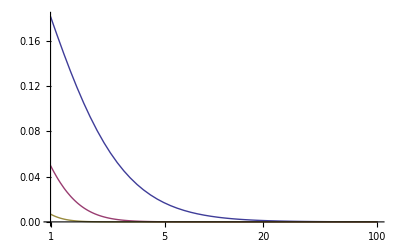

```mathematica
{F02}/.m->{2,5,10}/.θ->π/2;
LogLinearPlot[%,{R,1,100},PlotRange->{0,All}]
```